# Parallelschwingkreis

## Funktionen

### Includes

```mathematica
<<"Labor.m"
```

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ErrorBarLogPlots`"]
```

```mathematica
Gauss[a_]:= Module[{},{Mean[a],StandardDeviation[a]/Sqrt[Length[a]]}];
```

## Geräteliste

Oszi: HM400
true rms: Fluke 175

## 1.) Resonanzfrequenz (Bestimmung aus Amplituden- und Phasenverlauf)

### Induktivität und Kapazität

```mathematica
l={3,0}*10^-3;
rl=0.5;
c={0.1,0.01}*10^-6;
```

### Theoretische Resonanzfrequenz

```mathematica
(Elec`Fω[l[[1]],l[[2]],c[[1]],c[[2]]])/(2*π)
```

{9188.81,459.441}

```mathematica
1/(2*π)*√(1/(l[[1]]*c[[1]])-rl^2/l[[1]]^2)
```

9188.78

### Messung

```mathematica
{{"f/Hz", "Δf/Hz", "Ue/V", "ΔUe/V", "Ua/V", "ΔUa/V", "δt", "Δδt"}, {42.9, 0.1, 4, 0.4, 50*10^-3, 10*10^-3, 0.6*5*10^-3, 1*10^-3}, {94.8, 0.1, 2*2, 0.4, 1.7*50*10^-3, 10*10^-3, 2.1*10^-3, 10^-3/5}, {204.2, 0.1, 2*2, 0.4, 1.8*0.1, 0.02, 2.2*0.5*10^-3, 10^-3/5}, {438, 1, 4, 0.4, 1.8*0.2, 0.04, 0.5*10^-3, 10^-3/5}, {1510, 1, 2*2, 0.4, 2.6*0.5, 0.1, 2.6*50*10^-6, 10*10^-6}, {3016, 1, 2.2*2, 0.4, 2.6*1, 0.2, 1*50*10^-6, 10*10^-6}, {4410, 1, 2.5*2, 0.4, 3.6*1, 0.2, 1.2*20*10^-6, 4*10^-6}, {6750, 1, 2.8*2, 0.4, 2.5*2, 0.4, 0.4*20*10^-6, 4*10^-6}, {7.08*10^3, 10, 2.9*2, 0.4, 2.6*2, 0.4, 0.6*10*10^-6, 2*10^-6}, {8.17*10^3, 10, 3*2, 0.4, 2.8*2, 0.4, 1.2*2*10^-6, 0.4*10^-6}, {9.36*10^3, 10, 3*2, 0.4, 2.8*2, 0.4, 0, 0}, {10.17*10^3, 10, 3*2, 0.4, 2.8*2, 0.4, -0.3*5*10^-6, 10^-6}, {11.08*10^3, 10, 3*2, 0.4, 2.7*2, 0.4, -0.5*5*10^-6, 10^-6}, {12.15*10^3, 10, 2.6*2, 0.4, 2.9*2, 0.4, -0.6*5*10^-6, 10^-6}, {13.00*10^3, 10, 2.8*2, 0.4, 2.5*2, 0.4, -0.8*5*10^-6, 10^-6}, {14.20*10^3, 10, 2.8*2, 0.4, 2.4*2, 0.4, -0.9*5*10^-6, 10^-6}, {16.93*10^3, 10, 2.6*2, 0.4, 2.1*2, 0.4, -1*5*10^-6, 10^-6}, {43.60*10^3, 10, 2*2, 0.4, 3.4*0.5, 0.1, -0.8*5*10^-6, 10^-6}, {120.9*10^3, 100, 2*2, 0.4, 2.9*0.2, 0.04, -1.8*10^-6, 10^-6/5}, {418.6*10^3, 100, 2*2, 0.4, 1.2*0.1, 0.02, -1.2*0.5*10^-6, 0.1*10^-6}, {1012*10^3, 1000, 2*2, 0.4, 0.8*0.1, 0.02, 1.1*0.2*10^-6, 0.04*10^-6}}//TableForm //N
```

f/Hz | Δf/Hz | Ue/V | ΔUe/V | Ua/V | ΔUa/V | δt | Δδt
42.9 | 0.1 | 4. | 0.4 | 0.05 | 0.01 | 0.003 | 0.001
94.8 | 0.1 | 4. | 0.4 | 0.085 | 0.01 | 0.0021 | 0.0002
204.2 | 0.1 | 4. | 0.4 | 0.18 | 0.02 | 0.0011 | 0.0002
438. | 1. | 4. | 0.4 | 0.36 | 0.04 | 0.0005 | 0.0002
1510. | 1. | 4. | 0.4 | 1.3 | 0.1 | 0.00013 | 0.00001
3016. | 1. | 4.4 | 0.4 | 2.6 | 0.2 | 0.00005 | 0.00001
4410. | 1. | 5. | 0.4 | 3.6 | 0.2 | 0.000024 | 4.×10^-6
6750. | 1. | 5.6 | 0.4 | 5. | 0.4 | 8.×10^-6 | 4.×10^-6
7080. | 10. | 5.8 | 0.4 | 5.2 | 0.4 | 6.×10^-6 | 2.×10^-6
8170. | 10. | 6. | 0.4 | 5.6 | 0.4 | 2.4×10^-6 | 4.×10^-7
9360. | 10. | 6. | 0.4 | 5.6 | 0.4 | 0. | 0.
10170. | 10. | 6. | 0.4 | 5.6 | 0.4 | -1.5×10^-6 | 1.×10^-6
11080. | 10. | 6. | 0.4 | 5.4 | 0.4 | -2.5×10^-6 | 1.×10^-6
12150. | 10. | 5.2 | 0.4 | 5.8 | 0.4 | -3.×10^-6 | 1.×10^-6
13000. | 10. | 5.6 | 0.4 | 5. | 0.4 | -4.×10^-6 | 1.×10^-6
14200. | 10. | 5.6 | 0.4 | 4.8 | 0.4 | -4.5×10^-6 | 1.×10^-6
16930. | 10. | 5.2 | 0.4 | 4.2 | 0.4 | -5.×10^-6 | 1.×10^-6
43600. | 10. | 4. | 0.4 | 1.7 | 0.1 | -4.×10^-6 | 1.×10^-6
120900. | 100. | 4. | 0.4 | 0.58 | 0.04 | -1.8×10^-6 | 2.×10^-7
418600. | 100. | 4. | 0.4 | 0.12 | 0.02 | -6.×10^-7 | 1.×10^-7
1.012×10^6 | 1000. | 4. | 0.4 | 0.08 | 0.02 | 2.2×10^-7 | 4.×10^-8

```mathematica
M={{"f/Hz", "Ua/V", "δt", "Ue/V"}, {42.9, 50*10^-3, 0.6*5*10^-3, 4}, {94.8, 1.7*50*10^-3, 2.1*10^-3, 2*2}, {204.2, 1.8*0.1, 2.2*0.5*10^-3, 2*2}, {438, 1.8*0.2, 0.5*10^-3, 4}, {1510, 2.6*0.5, 2.6*50*10^-6, 2*2}, {3016, 2.6*1, 1*50*10^-6, 2.2*2}, {4410, 3.6*1, 1.2*20*10^-6, 2.5*2}, {6750, 2.5*2, 0.4*20*10^-6, 2.8*2}, {7.08*10^3, 2.6*2, 0.6*10*10^-6, 2.9*2}, {8.17*10^3, 2.8*2, 1.2*2*10^-6, 3*2}, {9.36*10^3, 2.8*2, 0, 3*2}, {10.17*10^3, 2.8*2, -0.3*5*10^-6, 3*2}, {11.08*10^3, 2.7*2, -0.5*5*10^-6, 3*2}, {13.00*10^3, 2.5*2, -0.8*5*10^-6, 2.8*2}, {14.20*10^3, 2.4*2, -0.9*5*10^-6, 2.8*2}, {16.93*10^3, 2.1*2, -1*5*10^-6, 2.6*2}, {43.60*10^3, 3.4*0.5, -0.8*5*10^-6, 2*2}, {120.9*10^3, 2.9*0.2, -1.8*10^-6, 2*2}, {418.6*10^3, 1.2*0.1, -1.2*0.5*10^-6, 2*2}}; dM={{"Δf/Hz", "ΔUa/V", "Δδt", "ΔUe/V"}, {0.1, 10*10^-3, 1*10^-3, 0.4}, {0.1, 10*10^-3, 10^-3/5, 0.4}, {0.1, 0.02, 10^-3/5, 0.4}, {1, 0.04, 10^-3/5, 0.4}, {1, 0.1, 10*10^-6, 0.4}, {1, 0.2, 10*10^-6, 0.4}, {1, 0.2, 4*10^-6, 0.4}, {1, 0.4, 4*10^-6, 0.4}, {10, 0.4, 2*10^-6, 0.4}, {10, 0.4, 0.4*10^-6, 0.4}, {10, 0.4, 0, 0.4}, {10, 0.4, 10^-6, 0.4}, {10, 0.4, 10^-6, 0.4}, {10, 0.4, 10^-6, 0.4}, {10, 0.4, 10^-6, 0.4}, {10, 0.4, 10^-6, 0.4}, {10, 0.1, 10^-6, 0.4}, {100, 0.04, 10^-6/5, 0.4}, {100, 0.02, 0.1*10^-6, 0.4}};
temp={{12.15*10^3, 2.9*2, -0.6*5*10^-6, 2.6*2}, {10, 0.4, 10^-6, 0.4}};
Ue=4;(*eff, fluke 175*)
due=0.4;
```

### Amplitudengang

```mathematica
(*{M[[2;;Length[M],1]],M[[2;;Length[M],2]]}*)
```

```mathematica
(*ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,AxesLabel-> {"f/Hz","Ua/Ue"}]*)
```

```mathematica
Table[{M[[x,1]],M[[x,2]]/M[[x,4]]},{x,2,Length[M]}]//TableForm//N
```

42.9 | 0.0125
94.8 | 0.02125
204.2 | 0.045
438. | 0.09
1510. | 0.325
3016. | 0.590909
4410. | 0.72
6750. | 0.892857
7080. | 0.896552
8170. | 0.933333
9360. | 0.933333
10170. | 0.933333
11080. | 0.9
13000. | 0.892857
14200. | 0.857143
16930. | 0.807692
43600. | 0.425
120900. | 0.145
418600. | 0.03

```mathematica
Gauss[{8170,9360,10170}]//N
```

{9233.33,580.814}

```mathematica
Gauss[{9233.33,9360}]
```

{9296.67,63.335}

```mathematica
Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}]//TableForm//N
```

42.9 | -43.8203
94.8 | -38.514
204.2 | -31.0109
438. | -24.0795
1510. | -11.2393
3016. | -5.26093
4410. | -3.28504
6750. | -1.13329
7080. | -1.09199
8170. | -0.689929
9360. | -0.689929
10170. | -0.689929
11080. | -1.05361
13000. | -1.13329
14200. | -1.54151
16930. | -2.13574
43600. | -8.55666
120900. | -19.3102
418600. | -35.0656

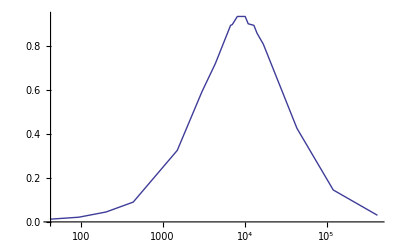

```mathematica
ListLogLinearPlot[Table[{M[[x,1]], M[[x,2]]/M[[x,4]]},{x,2,Length[M]}],Joined -> True]
```

```mathematica
At=Table[Basic`Fdiv[M[[x,2]],dM[[x,2]],M[[x,4]],dM[[x,4]]],{x,2,Length[M]}]
```

{{1/80,0.00375},{0.02125,0.004625},{0.045,0.0095},{0.09,0.019},{0.325,0.0575},{0.590909,0.0991736},{0.72,0.0976},{0.892857,0.135204},{0.896552,0.130797},{0.933333,0.128889},{0.933333,0.128889},{0.933333,0.128889},{0.9,0.126667},{0.892857,0.135204},{0.857143,0.132653},{0.807692,0.139053},{0.425,0.0675},{0.145,0.0245},{0.03,0.008}}

```mathematica
p1 = Table[{{M[[x,1]],10 Log[At[[x-1,1]]]},ErrorBar[dM[[x,1]],At[[x-1,2]]]},{x,2,Length[M]}]
```

{{{42.9,-10 Log[80]},ErrorBar[0.1,0.00375]},{{94.8,-38.514},ErrorBar[0.1,0.004625]},{{204.2,-31.0109},ErrorBar[0.1,0.0095]},{{438,-24.0795},ErrorBar[1,0.019]},{{1510,-11.2393},ErrorBar[1,0.0575]},{{3016,-5.26093},ErrorBar[1,0.0991736]},{{4410,-3.28504},ErrorBar[1,0.0976]},{{6750,-1.13329},ErrorBar[1,0.135204]},{{7080.,-1.09199},ErrorBar[10,0.130797]},{{8170.,-0.689929},ErrorBar[10,0.128889]},{{9360.,-0.689929},ErrorBar[10,0.128889]},{{10170.,-0.689929},ErrorBar[10,0.128889]},{{11080.,-1.05361},ErrorBar[10,0.126667]},{{13000.,-1.13329},ErrorBar[10,0.135204]},{{14200.,-1.54151},ErrorBar[10,0.132653]},{{16930.,-2.13574},ErrorBar[10,0.139053]},{{43600.,-8.55666},ErrorBar[10,0.0675]},{{120900.,-19.3102},ErrorBar[100,0.0245]},{{418600.,-35.0656},ErrorBar[100,0.008]}}

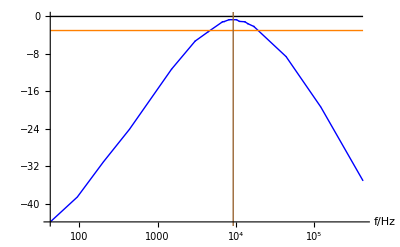

```mathematica
Show[ErrorListLogLinearPlot[p1,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9233.33,10},{9233.33,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz",""}]
```

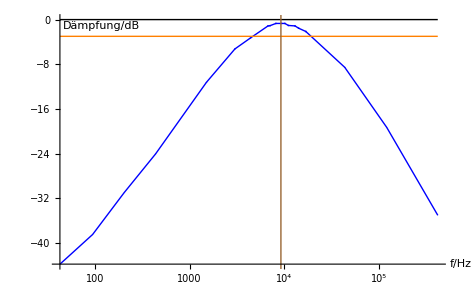

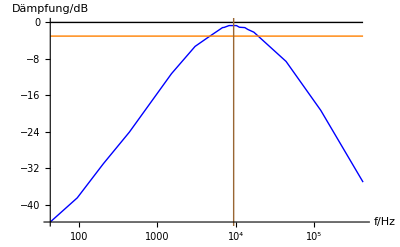

```mathematica
Show[ListLogLinearPlot[Table[{M[[x,1]],10 Log[M[[x,2]]/M[[x,4]]]},{x,2,Length[M]}],Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{-3},{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange,Black}],
ListLogLinearPlot[{{9360,10},{9360,-50}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel -> {"f/Hz","Dämpfung/dB"}]
```

### Phasengang

```mathematica
ϕ=Table[Basic`Fmult[M[[x,3]],dM[[x,3]],M[[x,1]],dM[[x,1]]]*360,{x,2,Length[M]}]//N
```

{{46.332,15.552},{71.6688,6.9012},{80.8632,14.742},{78.84,31.716},{70.668,5.4828},{54.288,10.8756},{38.1024,6.35904},{19.44,9.72288},{15.2928,5.1192},{7.05888,1.18512},{0.,0.},{-5.4918,3.6666},{-9.972,3.9978},{-18.72,4.6944},{-23.004,5.1282},{-30.474,6.1128},{-62.784,15.7104},{-78.3432,8.7696},{-90.4176,15.0912}}

```mathematica
p2 = Table[{{M[[x,1]],ϕ[[x-1,1]]},ErrorBar[dM[[x,1]],ϕ[[x-1,2]]]},{x,2,Length[M]}]
```

{{{42.9,46.332},ErrorBar[0.1,15.552]},{{94.8,71.6688},ErrorBar[0.1,6.9012]},{{204.2,80.8632},ErrorBar[0.1,14.742]},{{438,78.84},ErrorBar[1,31.716]},{{1510,70.668},ErrorBar[1,5.4828]},{{3016,54.288},ErrorBar[1,10.8756]},{{4410,38.1024},ErrorBar[1,6.35904]},{{6750,19.44},ErrorBar[1,9.72288]},{{7080.,15.2928},ErrorBar[10,5.1192]},{{8170.,7.05888},ErrorBar[10,1.18512]},{{9360.,0.},ErrorBar[10,0.]},{{10170.,-5.4918},ErrorBar[10,3.6666]},{{11080.,-9.972},ErrorBar[10,3.9978]},{{13000.,-18.72},ErrorBar[10,4.6944]},{{14200.,-23.004},ErrorBar[10,5.1282]},{{16930.,-30.474},ErrorBar[10,6.1128]},{{43600.,-62.784},ErrorBar[10,15.7104]},{{120900.,-78.3432},ErrorBar[100,8.7696]},{{418600.,-90.4176},ErrorBar[100,15.0912]}}

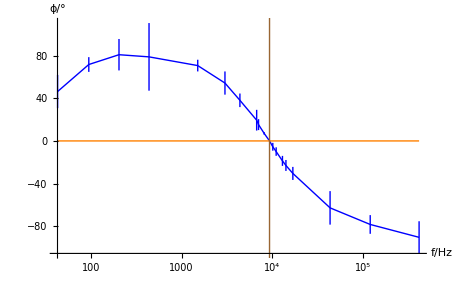

```mathematica
Show[ErrorListLogLinearPlot[p2,Joined-> True,PlotStyle-> {Blue}],
LogLinearPlot[{{0}},{x,Min[M[[2;;Length[M],1]]],Max[M[[2;;Length[M],1]]]},PlotStyle-> {Orange}],
ListLogLinearPlot[{{9360,-120},{9360,120}},Joined ->True,PlotStyle-> {Brown}],
AxesLabel-> {"f/Hz","ϕ/°"}]
```

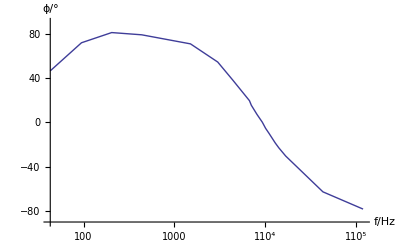

```mathematica
p3=Table[{M[[x,1]],M[[x,1]]*M[[x,3]]*360},{x,2,Length[M]-1}];
ListLogLinearPlot[p3,AxesLabel-> {"f/Hz","ϕ/°"},Joined-> True,PlotRange-> {{0,10^6},{-90,90}}]
```